### Figure 1 - transient period

```mathematica
μ=0.02; R0=17;
```

```mathematica
JacEE[p_]:={{-μ R0(1-p), -(365/22+μ)  }, {μ( R0(1-p)-1), 0}}
```

```mathematica
JacEEM[p_]:={{-μ R0(1-p), -(365/13+μ)  }, {μ( R0(1-p)-1), 0}}
```

```mathematica
JDFEP[p_]:={{-μ, -(365/22+μ) R0(1-p) }, {0, (365/22+μ)( R0(1-p)-1)}}
```

```mathematica
JDFEM[p_]:={{-μ, -(365/13+μ) R0(1-p) }, {0, (365/13+μ)( R0(1-p)-1)}}
```

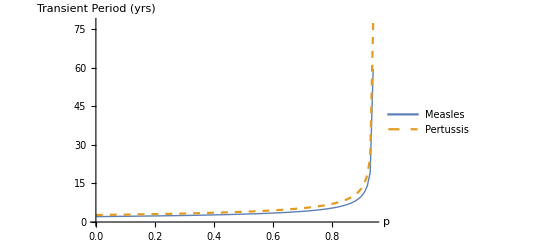

```mathematica
ListPlot[{Table[{p,2*π/(Abs[Im[Eigenvalues[JacEEM[p]][[1]]]])}, {p, 0, 1-1/R0, 0.01}], Table[{p,2*π/(Abs[Im[Eigenvalues[JacEE[p]][[1]]]])}, {p, 0, 1-1/R0, 0.01}]}, PlotLegends->Placed[{"Measles", "Pertussis"}, {0.25, 0.75}],PlotStyle->{Thick, Dashed}, AxesLabel->{"p", "Transient Period (yrs)"}, PlotRange->All, Joined->True]
```

```mathematica
Export["Transientperiod.pdf", %]
```

Transientperiod.pdf

### Figure 2: amplification envelope

```mathematica
R0=17; γ=365/22; μ=0.02; p=1-1/R0+0.01;JDFEp={{-μ, -(γ+μ) R0(1-p) }, {0, (γ+μ)( R0(1-p)-1)}}
```

{{-0.02,-13.7871},{0,-2.82385}}

```mathematica
AmpEnvelopePDFE[p_]:=Module[{},R0=17; γ=365/22; μ=0.02; JDFEp={{-μ, -(γ+μ) R0(1-p) }, {0, (γ+μ)( R0(1-p)-1)}};Return[Max[Table[SingularValueList[MatrixExp[JDFEp t],1][[1]], {t, 0, 10, 0.01}]]]]
```

```mathematica
AmpEnvelopeMDFE[p_]:=Module[{},γ=365/13;R0=17;  μ=0.02; JDFEp={{-μ, -(γ+μ) R0(1-p) }, {0, (γ+μ)( R0(1-p)-1)}};Return[Max[Table[SingularValueList[MatrixExp[JDFEp t],1][[1]], {t, 0, 10, 0.01}]]]]
```

```mathematica
AmpEnvelopePtab[p_]:=Module[{},γ=365/22;JEEp={{-μ R0(1-p), -(γ+μ)  }, {μ( R0(1-p)-1), 0}};Return[Table[SingularValueList[MatrixExp[JEEp t],1][[1]], {t, 0, 10, 0.01}]]]
```

```mathematica
AmpEnvelopeP[p_]:=Module[{},γ=365/22;JEEp={{-μ R0(1-p), -(γ+μ)  }, {μ( R0(1-p)-1), 0}};Return[Max[Table[SingularValueList[MatrixExp[JEEp t],1][[1]], {t, 0, 10, 0.01}]]]]
```

```mathematica
AmpEnvelopeM[p_]:=Module[{},γ=365/13;JEEp={{-μ R0(1-p), -(γ+μ)  }, {μ( R0(1-p)-1), 0}};Return[Max[Table[SingularValueList[MatrixExp[JEEp t],1][[1]], {t, 0, 10, 0.01}]]]]
```

```mathematica
AmpEnvelopePDFETime[p_]:=Module[{},γ=365/22;JDFEp={{-μ, -(γ+μ) R0(1-p) }, {0, (γ+μ)( R0(1-p)-1)}};
tab=Table[Norm[MatrixExp[JDFEp*t]], {t, 0, 10, 0.01}];
maxtime=Position[tab, Max[tab]][[1]][[1]];
Return[Range[0,10,0.01][[maxtime]]]]
```

```mathematica
AmpEnvelopeMDFETime[p_]:=Module[{},γ=365/13;JDFEp={{-μ, -(γ+μ) R0(1-p) }, {0, (γ+μ)( R0(1-p)-1)}};
tab=Table[Norm[MatrixExp[JDFEp*t]], {t, 0, 10, 0.01}];
maxtime=Position[tab, Max[tab]][[1]][[1]];
Return[Range[0,10,0.01][[maxtime]]]]
```

```mathematica
AmpEnvelopePTime[p_]:=Module[{},γ=365/22;JEEp={{-μ R0(1-p), -(γ+μ)  }, {μ( R0(1-p)-1), 0}};
tab=Table[Norm[MatrixExp[JEEp*t]], {t, 0, 10, 0.01}];
maxtime=Position[tab, Max[tab]][[1]][[1]];
Return[Range[0,10,0.01][[maxtime]]]]
```

```mathematica
AmpEnvelopeMTime[p_]:=Module[{},γ=365/13;JEEp={{-μ R0(1-p), -(γ+μ)  }, {μ( R0(1-p)-1), 0}};
tab=Table[Norm[MatrixExp[JEEp*t]], {t, 0, 10, 0.01}];
maxtime=Position[tab, Max[tab]][[1]][[1]];
Return[Range[0,10,0.01][[maxtime]]]]
```

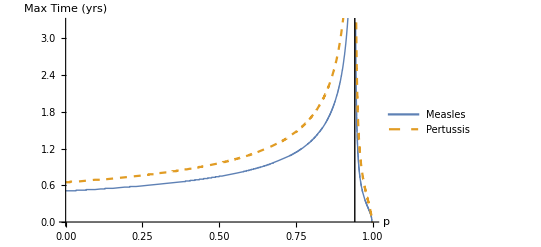

```mathematica
timeplot=Show[Plot[{AmpEnvelopeMDFETime[p],AmpEnvelopePDFETime[p]},  {p,1-1/R0, 0.999}, PlotStyle->{Thick, Dashed}, AxesOrigin->{0,0}, PlotLegends->Placed[{"Measles", "Pertussis"},{0.25,0.75}],AxesLabel->{"p", "Max Time (yrs)"}], Plot[{AmpEnvelopeMTime[p], AmpEnvelopePTime[p]}, {p,0,1-1/R0},PlotStyle->{Thick, Dashed}, PlotRange->All], Graphics[Line[{{1-1/R0, 0}, {1-1/R0, 4}}]]]
```

```mathematica
Export["AmpEnvelopeTime.pdf",timeplot]
```

AmpEnvelopeTime.pdf

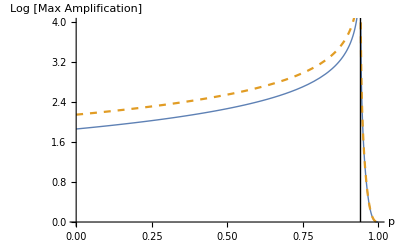

```mathematica
ampenvplot=Show[Plot[{Log[AmpEnvelopePDFE[p]],Log[AmpEnvelopeMDFE[p]]},  {p,1-1/R0, 0.999}, PlotStyle->{Thick, Dashed}, AxesOrigin->{0,0},  PlotRange->{0,4},AxesLabel->{"p", "Log [Max Amplification]"}], Plot[{Log[AmpEnvelopeP[p]], Log[AmpEnvelopeM[p]]}, {p,0,1-1/R0}, PlotStyle->{Thick, Dashed},PlotRange->All, Epilog->Text[Style["(a)",FontFamily->"Arial",12, Bold], {0.1,3}]], Graphics[Line[{{1-1/R0, 0}, {1-1/R0, 7}}]]]
```

```mathematica
Export["AmpEnvelope.pdf",ampenvplot]
```

AmpEnvelope.pdf

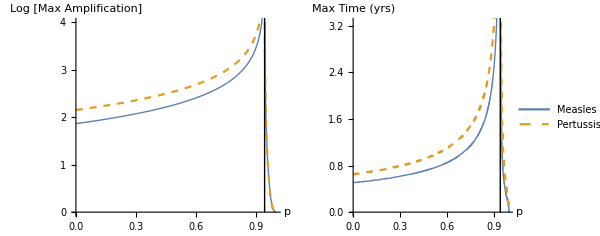

```mathematica
GraphicsRow[{ampenvplot, timeplot}, AspectRatio->Automatic,Spacings->20, ImageSize->600]
```

```mathematica
Export["AmpEnvelopeRow.pdf",%]
```

AmpEnvelopeRow.pdf